## Plotting parameters

Where to save plots

```mathematica
SetDirectory[NotebookDirectory[]]; (*sets current directory to be location of this file*)
plotdir="Plots/";(*directory to save figures in*)
```

NotebookDirectory::nosv: The notebook 2xk_shm is not saved.

SetDirectory::fstr: File specification $Failed is not a string of one or more characters.

Remove lines from region plots when saving

```mathematica
rasterTrick[plot_]:=Show[plot,Prolog->{Opacity[0],Texture[{{{0,0,0,0}}}],VertexTextureCoordinates->{{0,0},{1,0},{1,1}},Polygon[{{0,0},{.1,0},{.1,.1}}]}]
```

Universal aesthetics

```mathematica
lwd=0.006;(*line thickness as fraction of plot width*)
letpos = {0.05,0.95}; (*relative location of panel letter*)
ylabpos={-0.16,0.5};  (*relative location of y axis label*)
ylabposregion={-0.1,0.5};(*for region plots*)
inches=72;
xsize=5inches; (*width of panel*)
aspectratio=1/Sqrt[2]; (*aspect ratio of panel*)
ticksize={0,0.01}; (*size of tick marks*)
pad={{50,20},{40,20}};  (*white space around plot {{left,right},{bottom,top}}*)
padregion={{40,10},{40,30}};  (*white space around region plot {{left,right},{bottom,top}}*)
posplotscale=1;
```

Basic plot style (λ vs cM plots)

```mathematica
Clear[plotstyle]
plotstyle[xmin_,xmax_,xtickmin_,xtickmax_,xint_,ymin_,ymax_,ytickmin_,ytickmax_,yint_]:={
PlotRange->{{xmin,xmax},{ymin,ymax}},
ImageSize->{xsize *posplotscale,xsize aspectratio*posplotscale},
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xtickmin,xtickmax,xint}],Table[{y,y,ticksize},{y,ytickmin,ytickmax,yint}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
BaseStyle->{FontFamily->"Helvetica",FontSize->14 *posplotscale},
ImagePadding->pad,
PlotRangeClipping->False
}
```

Log-linear plot style (λ vs R plots)

```mathematica
Clear[loglinearplotstyle]
loglinearplotstyle[xmin_,xmax_,xmarks_,ymin_,ymax_,ytickmin_,ytickmax_,yint_,recrate_]:={
PlotRange->{Log@{xmin,xmax},{ymin,ymax}},
ImageSize->{xsize*posplotscale,xsize aspectratio *posplotscale},
AspectRatio->aspectratio,
PlotRangePadding->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{Table[{y,y,ticksize},{y,ytickmin,ytickmax,yint}],None},{Append[Table[{Log@x,x,ticksize},{x,xmarks}],{Log@recrate,"r",ticksize}],None}},
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameStyle->Directive[Black,Thickness[lwd]],
BaseStyle->{FontFamily->"Helvetica",FontSize->14*posplotscale},
ImagePadding->pad
}
```

Log-linear inset plot style (frequency dynamics)

```mathematica
Clear[insetloglinearplotstyle]
insetloglinearplotstyle[xmin_,xmax_,xmarks_,ymin_,ymax_,ytickmin_,ytickmax_,yint_]:={
PlotRange->{Log@{xmin,xmax},{ymin,ymax}},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{Table[{y,y,ticksize},{y,ytickmin,ytickmax,yint}],None},{Table[{Log@x,x,ticksize},{x,xmarks}],None}},
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameStyle->Directive[Black,Thickness[lwd]],
BaseStyle->{FontFamily->"Helvetica",FontSize->8*4/5},
ImagePadding->pad
}
```

Region plot style (where neo-W invades)

```mathematica
Clear[regionplotstyle]
regionplotstyle[xmin_,xmax_,xtickmin_,xtickmax_,xint_,ymin_,ymax_,ytickmin_,ytickmax_,yint_]:={
PlotRange->{{xmin,xmax},{ymin,ymax}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xtickmin,xtickmax,xint}],Table[{y,y,ticksize},{y,ytickmin,ytickmax,yint}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->padregion,
PlotRangeClipping->False
}
```

## Useful functions

### XY resident equilibrium and stability

Resident equilibria

```mathematica
(*differenceEqs//Simplify*)
```

```mathematica
Clear[equilXY]
equilXY[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_]:=equilXY[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]={pXf,pXm,pYm,q}/.NSolve[{(Faa pXf (-1+pXf+pXm-pXf pXm) waf wam-FAA (-1+pXf) pXf pXm wAf wAm+FAa (-pXm waf wAm+pXf ((-1+pXm) wAf wam+pXm waf wAm)) (pXf-αf))/(Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm))),(2 Maa (-1+pXf) pXm (-1+pYm) (-1+q) waf wam+MAA pXf pYm (1+2 pXm (-1+q)) wAf wAm-2 MAa (pYm waf wAm (pXm-pXm q-r αm)+pXf (pXm (-1+q) ((-1+pYm) wAf wam+pYm waf wAm)+((-1+pYm+r-pYm r) wAf wam+pYm r waf wAm) αm)))/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm)))),(-2 Maa (-1+pXf) (-1+pYm) pYm q waf wam+MAA pXf pYm (1-2 pYm q) wAf wAm+2 MAa (pYm waf wAm (-pYm q+αm-r αm)+pXf (pYm^2 q (wAf wam+waf wAm)+r wAf wam αm-pYm (q wAf wam+r wAf wam αm+waf wAm αm-r waf wAm αm))))/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm)))),(-Maa (-1+pXf) (-1+pYm) (-1+2 q) waf wam+MAA pXf pYm (1-2 q) wAf wAm+2 MAa (pYm waf wAm (-q+r+αm-2 r αm)+pXf ((-1+pYm) wAf wam (-1+q+r+αm-2 r αm)+pYm waf wAm (q-αm+r (-1+2 αm)))))/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))}=={0,0,0,0},{pXf,pXm,pYm,q}]
```

Eigenvalues of internal stability matrix

```mathematica
(*matIntFull//Simplify*)
```

```mathematica
Clear[internstabXY];
internstabXY[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,pXf_,pXm_,pYm_,q_]:=internstabXY[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,pXf,pXm,pYm,q]=Eigenvalues[{{(waf wAf (-FAa FAA pXm^2 wAm^2 (-1+αf)-Faa (-1+pXm) wam (FAA pXm wAm-FAa (-1+pXm) wam αf)))/(Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm)))^2,(wam wAm (-FAa FAA pXf^2 wAf^2 (-1+αf)-Faa (-1+pXf) waf (FAA pXf wAf-FAa (-1+pXf) waf αf)))/(Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm)))^2,0},{-(waf wAf (Maa (-1+pYm) wam (MAA pYm wAm+2 MAa (-1+pYm) (-1+r) wam αm)+2 MAa pYm wAm (-1+αm) (-MAA pYm (-1+r) wAm+2 MAa (-1+pYm) (-1+2 r) wam αm)))/(Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+2 MAa (pYm waf wAm (1-αm+r (-1+2 αm))+pXf (wAf wam αm+r ((-1+pYm) wAf wam-pYm waf wAm) (-1+2 αm)+pYm (waf wAm (-1+αm)-wAf wam αm))))^2,0,(wam wAm (-Maa (-1+pXf) waf (MAA pXf wAf-2 MAa (-1+pXf) r waf αm)+2 MAa pXf wAf (-1+αm) (-MAA pXf r wAf+2 MAa (-1+pXf) (-1+2 r) waf αm)))/(Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+2 MAa (pYm waf wAm (1-αm+r (-1+2 αm))+pXf (wAf wam αm+r ((-1+pYm) wAf wam-pYm waf wAm) (-1+2 αm)+pYm (waf wAm (-1+αm)-wAf wam αm))))^2},{(waf wAf (-Maa (-1+pYm) wam (MAA pYm wAm-2 MAa (-1+pYm) r wam αm)+2 MAa pYm wAm (-1+αm) (-MAA pYm r wAm+2 MAa (-1+pYm) (-1+2 r) wam αm)))/(Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm-2 MAa (pYm waf wAm (-αm+r (-1+2 αm))+pXf (pYm waf wAm (r+αm-2 r αm)+(-1+pYm) wAf wam (1-r-αm+2 r αm))))^2,0,-(wam wAm (Maa (-1+pXf) waf (MAA pXf wAf+2 MAa (-1+pXf) (-1+r) waf αm)+2 MAa pXf wAf (-1+αm) (-MAA pXf (-1+r) wAf+2 MAa (-1+pXf) (-1+2 r) waf αm)))/(Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm-2 MAa (pYm waf wAm (-αm+r (-1+2 αm))+pXf (pYm waf wAm (r+αm-2 r αm)+(-1+pYm) wAf wam (1-r-αm+2 r αm))))^2}}]
```

The following uses this cutoff to avoid numerical problems

```mathematica
cutoff=10^(-12);
```

Restricting answers to cases of polymorphic equilibria that are internally stable

```mathematica
Clear[sieveXY]
sieveXY[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_]:=sieveXY[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]=Block[{},For[i=1; write={},i≤(max=Length[eq=equilXY[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]]),i++,
If[Length[test=Cases[eq[[i]],x_/;((-cutoff≤Re[x]≤1+cutoff)&&Abs[Im[x]]<cutoff)]]==4&&(Chop[eq[[i]]]≠{0,0,0,})&&(Chop[eq[[i]]-{1,1,1,1}]≠{0,0,0,})&&
(Max[Abs[internstabXY[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,eq[[i,1]],eq[[i,2]],eq[[i,3]],eq[[i,4]]]]]<1),write=Append[write,eq[[i]]]]];
Sort[write]
]
```

### Invasion of neo-W into XY

Invasion fitness (external stability)

```mathematica
(*charpolyk1//Simplify*)
```

```mathematica
Clear[invasionplotXY]
invasionplotXY[tryFAA_,tryFAa_,tryFaa_,tryMAA_,tryMAa_,tryMaa_,trywAf_,trywaf_,trywAm_,trywam_,tryαf_,tryαm_,tryr_,tryR_,tryρ_]:=
Block[{valideq,temp,pXf,pXm,pYf,pYm,q,subs,r,R,ρ},
valideq=sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr];
If[Length[valideq]==1,
temp=Flatten[valideq];
pXf=temp[[1]];
pXm=temp[[2]];
pYf=0;
pYm=temp[[3]];
q=temp[[4]];
subs={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf-> tryαf,αm-> tryαm};
r=tryr;
R=tryR;
ρ=tryρ;
Max[λ/.NSolve[0==(λ^4 (2 Faa^2 (-1+pXf) (-1+pXm) (-1+q) waf^2 wam^2 λ (1-pYm q-2 λ+2 pXf λ+2 q λ-2 pXf q λ+pXm (-1+q) (1+2 (-1+pXf) λ))-Faa waf wam (FAA wAf wAm (pYm q (-1+pYm q+2 (-1+pXf) (-1+q) λ)-pXm^2 (-1+q)^2 (-1+2 λ+8 (-1+pXf) pXf λ^2)+pXm (-1+q) (1+2 pYm q (-1+λ)-2 (1+(-1+pXf) q) λ+8 (-1+pXf) pXf (-1+q) λ^2))+2 FAa (wAf wam ((1+pXm (-1+q)-pYm q) (-1+R) αf (1-pYm q-2 λ+2 pXf λ+2 q λ-2 pXf q λ+pXm (-1+q) (1+2 (-1+pXf) λ))+pXf (-1+pXm) (-1+q) λ (1-pYm q-4 λ+4 pXf λ+4 q λ-4 pXf q λ+pXm (-1+q) (1+4 (-1+pXf) λ)))+(-1+pXf) (-1+q) waf wAm λ (2 pYm q (-1+R) (-1+αf)+pXm^2 (-1+q) (3+2 R (-1+αf)-2 αf-4 λ+4 pXf λ)+pXm (3+2 R (-1+αf)-2 αf-4 λ+4 pXf λ+q (pYm (-3+2 R+2 αf-2 R αf)+2 (-1+R+αf-R αf+2 λ-2 pXf λ))))))+2 (FAA^2 pXf pXm (-1+q) wAf^2 wAm^2 λ (pYm q+pXm (-1+q) (-1+2 pXf λ))-FAa FAA wAf wAm (pYm q (pYm q waf wAm (-1+R+αf-R αf)-pXf (-1+q) wAf wam λ)+pXm^2 (-1+q)^2 (pXf wAf wam λ (-1+2 (-1+R) αf+4 pXf λ)+waf wAm (-1+αf+λ+pXf λ-2 pXf αf λ-4 pXf λ^2+4 pXf^2 λ^2+R (-1+αf) (-1+2 pXf λ)))-pXm (-1+q) (pXf wAf wam λ (1+2 αf-2 R αf-4 pXf λ+q (-1+4 pXf λ))+pYm q (pXf wAf wam (-1+2 (-1+R) αf) λ+waf wAm (-2+2 αf+λ+pXf λ-2 pXf αf λ+2 R (-1+αf) (-1+pXf λ)))))+2 FAa^2 (wAf wam (pYm^2 q^2 waf wAm αf (-1-2 R (-1+αf)+αf)+pXf (-1+q) wAf wam λ (αf-R αf+pXf (-1+q) λ)+pYm q (pXf (-1+q) (-1+R) wAf wam αf λ+waf wAm (-1+αf) ((-1+2 R) αf+pXf (-1+q) (-1+R) λ)))+pXm^2 (-1+q)^2 (pXf wAf^2 wam^2 λ ((-1+R) αf+pXf λ)+(-1+pXf) waf^2 wAm^2 λ (1+R (-1+αf)-αf-λ+pXf λ)+waf wAf wam wAm ((1-2 R) αf^2+pXf λ (1-R+2 (-1+pXf) λ)+αf (-1+λ-2 pXf λ+R (2+(-1+2 pXf) λ))))-pXm (-1+q) ((-1+pXf) pYm q (-1+R) waf^2 wAm^2 (-1+αf) λ+pXf wAf^2 wam^2 λ ((-2+q+pYm q) (-1+R) αf+2 pXf (-1+q) λ)+waf wAf wam wAm (-(-1+2 pYm q) (-1+2 R) αf^2+pXf λ (-1+R+2 λ-2 pXf λ+q (1+pYm-R-pYm R-2 λ+2 pXf λ))+αf (1-λ+2 pXf λ-pXf q λ+R (-2+λ-2 pXf λ+pXf q λ)+pYm q (-2+λ-2 pXf λ+R (4-λ+2 pXf λ)))))))) (2 Faa^2 (-1+pXf) (-1+pXm) (-1+q) waf^2 wam^2 λ (1-2 λ+2 pXf λ+2 q λ-2 pXf q λ+pXm (-1+q) (1+2 (-1+pXf) λ-ρ)+pYm q (-1+ρ)-ρ)+2 FAA^2 pXf pXm (-1+q) wAf^2 wAm^2 λ (-pYm q (-1+ρ)+pXm (-1+q) (-1+2 pXf λ+ρ))-FAa FAA wAf wAm (pYm q (-1+ρ) (2 pXf (-1+q) wAf wam λ+pYm q waf wAm (-1+αf) (-2+r+R+ρ))+pXm^2 (-1+q)^2 (2 pXf wAf wam λ (-1+4 pXf λ+ρ+αf (-2+r+R+ρ))+waf wAm (-2+2 αf+2 λ+2 pXf λ-4 pXf αf λ-8 pXf λ^2+8 pXf^2 λ^2+3 ρ-3 αf ρ-2 λ ρ+2 pXf αf λ ρ-ρ^2+αf ρ^2+r (-1+αf) (-1+2 pXf λ+ρ)+R (-1+αf) (-1+2 pXf λ+ρ)))-2 pXm (-1+q) (pXf wAf wam λ (1-4 pXf λ-ρ-αf (-2+r+R+ρ)+q (-1+4 pXf λ+ρ))+pYm q (pXf wAf wam λ (-1+ρ+αf (-2+r+R+ρ))+waf wAm (-2+2 αf+λ+pXf λ-2 pXf αf λ+3 ρ-3 αf ρ-λ ρ+pXf αf λ ρ-ρ^2+αf ρ^2+r (-1+αf) (-1+pXf λ+ρ)+R (-1+αf) (-1+pXf λ+ρ)))))+2 FAa^2 (pXm^2 (-1+q)^2 ((-1+pXf) waf^2 wAm^2 λ (2+r (-1+αf)+R (-1+αf)-2 αf-2 λ+2 pXf λ-ρ+αf ρ)+pXf wAf^2 wam^2 λ (2 pXf λ+αf (-2+r+R+ρ))+waf wAf wam wAm (pXf λ (2-r-R-4 λ+4 pXf λ-ρ)+2 (-1+r+R) αf^2 (-1+ρ)+αf (-2+2 λ-4 pXf λ+R (2-λ+2 pXf λ-2 ρ)+r (2+(-1+2 pXf) λ-2 ρ)+2 ρ-λ ρ+2 pXf λ ρ)))+wAf wam (2 pYm^2 q^2 (-1+r+R) waf wAm (-1+αf) αf (-1+ρ)-pXf (-1+q) wAf wam λ (-2 pXf (-1+q) λ+αf (-2+r+R+ρ))+pYm q (pXf (-1+q) wAf wam αf λ (-2+r+R+ρ)-waf wAm (-1+αf) (2 (-1+r+R) αf (-1+ρ)-pXf (-1+q) λ (-2+r+R+ρ))))-pXm (-1+q) ((-1+pXf) pYm q waf^2 wAm^2 (-1+αf) λ (-2+r+R+ρ)+pXf wAf^2 wam^2 λ (4 pXf (-1+q) λ+(-2+q+pYm q) αf (-2+r+R+ρ))+waf wAf wam wAm (2 (-1+2 pYm q) (-1+r+R) αf^2 (-1+ρ)+αf (2-2 R-2 λ+4 pXf λ-2 pXf q λ+R λ-2 pXf R λ+pXf q R λ-2 ρ+2 R ρ+λ ρ-2 pXf λ ρ+pXf q λ ρ+r (-2+λ-2 pXf λ+pXf q λ+2 ρ)+pYm q (-4+2 λ-4 pXf λ+R (4-λ+2 pXf λ-4 ρ)+r (4+(-1+2 pXf) λ-4 ρ)+4 ρ-λ ρ+2 pXf λ ρ))+pXf λ (-2+r+R+4 λ-4 pXf λ+ρ-q (-2+r+R+4 λ-4 pXf λ+ρ+pYm (-2+r+R+ρ))))))+Faa waf wam (FAA wAf wAm (pXm^2 (-1+q)^2 (8 (-1+pXf) pXf λ^2-2 λ (-1+ρ)-(-1+ρ)^2)-pYm q (1+2 (-1+pXf+q-pXf q) λ+pYm q (-1+ρ)-ρ) (-1+ρ)+pXm (-1+q) (-8 (-1+pXf) pXf (-1+q) λ^2-2 (1+(-1+pXf) q) λ (-1+ρ)-(-1+ρ)^2+2 pYm q (-1+ρ) (-1+λ+ρ)))+FAa (wAf wam (-2 pXf (-1+pXm) (-1+q) λ (1-4 λ+4 pXf λ+4 q λ-4 pXf q λ+pXm (-1+q) (1+4 (-1+pXf) λ-ρ)+pYm q (-1+ρ)-ρ)+(1+pXm (-1+q)-pYm q) αf (-2+r+R+ρ) (-1+2 λ-2 pXf λ-2 q λ+2 pXf q λ-pXm (-1+q) (1+2 (-1+pXf) λ-ρ)+ρ+pYm (q-q ρ)))-2 (-1+pXf) (-1+q) waf wAm λ (pYm q (-1+αf) (-2+r+R+ρ)+pXm^2 (-1+q) (3+r (-1+αf)+R (-1+αf)-2 αf-4 λ+4 pXf λ-2 ρ+αf ρ)-pXm (-3+r+R+2 αf-r αf-R αf+4 λ-4 pXf λ+2 ρ-αf ρ+q (2-R+r (-1+αf)-2 αf+R αf-4 λ+4 pXf λ-ρ+αf ρ+pYm (3+r (-1+αf)+R (-1+αf)-2 αf-2 ρ+αf ρ))))))))/(16 (-1+q)^4 (Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm)))^4)/.subs,λ]]-1
]
]
```

### Invasion of neo-W into XY (allows two equilibria)

```mathematica
Clear[invasionplotXY2]
invasionplotXY2[{tryFAA_,tryFAa_,tryFaa_,tryMAA_,tryMAa_,tryMaa_,tryFA_,tryFa_,tryMA_,tryMa_,tryFdA_,tryMdA_,tryr_,tryR_,tryρ_},{pXf_,pXm_,pYm_,q_}]:=
Block[{subs,r,R,ρ},
subs={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->tryFA,waf->tryFa,wAm->tryMA,wam->tryMa,αf-> tryFdA,αm-> tryMdA};
r=tryr;
R=tryR;
ρ=tryρ;
Max[λ/.NSolve[0==0==(λ^4 (2 Faa^2 (-1+pXf) (-1+pXm) (-1+q) waf^2 wam^2 λ (1-pYm q-2 λ+2 pXf λ+2 q λ-2 pXf q λ+pXm (-1+q) (1+2 (-1+pXf) λ))-Faa waf wam (FAA wAf wAm (pYm q (-1+pYm q+2 (-1+pXf) (-1+q) λ)-pXm^2 (-1+q)^2 (-1+2 λ+8 (-1+pXf) pXf λ^2)+pXm (-1+q) (1+2 pYm q (-1+λ)-2 (1+(-1+pXf) q) λ+8 (-1+pXf) pXf (-1+q) λ^2))+2 FAa (wAf wam ((1+pXm (-1+q)-pYm q) (-1+R) αf (1-pYm q-2 λ+2 pXf λ+2 q λ-2 pXf q λ+pXm (-1+q) (1+2 (-1+pXf) λ))+pXf (-1+pXm) (-1+q) λ (1-pYm q-4 λ+4 pXf λ+4 q λ-4 pXf q λ+pXm (-1+q) (1+4 (-1+pXf) λ)))+(-1+pXf) (-1+q) waf wAm λ (2 pYm q (-1+R) (-1+αf)+pXm^2 (-1+q) (3+2 R (-1+αf)-2 αf-4 λ+4 pXf λ)+pXm (3+2 R (-1+αf)-2 αf-4 λ+4 pXf λ+q (pYm (-3+2 R+2 αf-2 R αf)+2 (-1+R+αf-R αf+2 λ-2 pXf λ))))))+2 (FAA^2 pXf pXm (-1+q) wAf^2 wAm^2 λ (pYm q+pXm (-1+q) (-1+2 pXf λ))-FAa FAA wAf wAm (pYm q (pYm q waf wAm (-1+R+αf-R αf)-pXf (-1+q) wAf wam λ)+pXm^2 (-1+q)^2 (pXf wAf wam λ (-1+2 (-1+R) αf+4 pXf λ)+waf wAm (-1+αf+λ+pXf λ-2 pXf αf λ-4 pXf λ^2+4 pXf^2 λ^2+R (-1+αf) (-1+2 pXf λ)))-pXm (-1+q) (pXf wAf wam λ (1+2 αf-2 R αf-4 pXf λ+q (-1+4 pXf λ))+pYm q (pXf wAf wam (-1+2 (-1+R) αf) λ+waf wAm (-2+2 αf+λ+pXf λ-2 pXf αf λ+2 R (-1+αf) (-1+pXf λ)))))+2 FAa^2 (wAf wam (pYm^2 q^2 waf wAm αf (-1-2 R (-1+αf)+αf)+pXf (-1+q) wAf wam λ (αf-R αf+pXf (-1+q) λ)+pYm q (pXf (-1+q) (-1+R) wAf wam αf λ+waf wAm (-1+αf) ((-1+2 R) αf+pXf (-1+q) (-1+R) λ)))+pXm^2 (-1+q)^2 (pXf wAf^2 wam^2 λ ((-1+R) αf+pXf λ)+(-1+pXf) waf^2 wAm^2 λ (1+R (-1+αf)-αf-λ+pXf λ)+waf wAf wam wAm ((1-2 R) αf^2+pXf λ (1-R+2 (-1+pXf) λ)+αf (-1+λ-2 pXf λ+R (2+(-1+2 pXf) λ))))-pXm (-1+q) ((-1+pXf) pYm q (-1+R) waf^2 wAm^2 (-1+αf) λ+pXf wAf^2 wam^2 λ ((-2+q+pYm q) (-1+R) αf+2 pXf (-1+q) λ)+waf wAf wam wAm (-(-1+2 pYm q) (-1+2 R) αf^2+pXf λ (-1+R+2 λ-2 pXf λ+q (1+pYm-R-pYm R-2 λ+2 pXf λ))+αf (1-λ+2 pXf λ-pXf q λ+R (-2+λ-2 pXf λ+pXf q λ)+pYm q (-2+λ-2 pXf λ+R (4-λ+2 pXf λ)))))))) (2 Faa^2 (-1+pXf) (-1+pXm) (-1+q) waf^2 wam^2 λ (1-2 λ+2 pXf λ+2 q λ-2 pXf q λ+pXm (-1+q) (1+2 (-1+pXf) λ-ρ)+pYm q (-1+ρ)-ρ)+2 FAA^2 pXf pXm (-1+q) wAf^2 wAm^2 λ (-pYm q (-1+ρ)+pXm (-1+q) (-1+2 pXf λ+ρ))-FAa FAA wAf wAm (pYm q (-1+ρ) (2 pXf (-1+q) wAf wam λ+pYm q waf wAm (-1+αf) (-2+r+R+ρ))+pXm^2 (-1+q)^2 (2 pXf wAf wam λ (-1+4 pXf λ+ρ+αf (-2+r+R+ρ))+waf wAm (-2+2 αf+2 λ+2 pXf λ-4 pXf αf λ-8 pXf λ^2+8 pXf^2 λ^2+3 ρ-3 αf ρ-2 λ ρ+2 pXf αf λ ρ-ρ^2+αf ρ^2+r (-1+αf) (-1+2 pXf λ+ρ)+R (-1+αf) (-1+2 pXf λ+ρ)))-2 pXm (-1+q) (pXf wAf wam λ (1-4 pXf λ-ρ-αf (-2+r+R+ρ)+q (-1+4 pXf λ+ρ))+pYm q (pXf wAf wam λ (-1+ρ+αf (-2+r+R+ρ))+waf wAm (-2+2 αf+λ+pXf λ-2 pXf αf λ+3 ρ-3 αf ρ-λ ρ+pXf αf λ ρ-ρ^2+αf ρ^2+r (-1+αf) (-1+pXf λ+ρ)+R (-1+αf) (-1+pXf λ+ρ)))))+2 FAa^2 (pXm^2 (-1+q)^2 ((-1+pXf) waf^2 wAm^2 λ (2+r (-1+αf)+R (-1+αf)-2 αf-2 λ+2 pXf λ-ρ+αf ρ)+pXf wAf^2 wam^2 λ (2 pXf λ+αf (-2+r+R+ρ))+waf wAf wam wAm (pXf λ (2-r-R-4 λ+4 pXf λ-ρ)+2 (-1+r+R) αf^2 (-1+ρ)+αf (-2+2 λ-4 pXf λ+R (2-λ+2 pXf λ-2 ρ)+r (2+(-1+2 pXf) λ-2 ρ)+2 ρ-λ ρ+2 pXf λ ρ)))+wAf wam (2 pYm^2 q^2 (-1+r+R) waf wAm (-1+αf) αf (-1+ρ)-pXf (-1+q) wAf wam λ (-2 pXf (-1+q) λ+αf (-2+r+R+ρ))+pYm q (pXf (-1+q) wAf wam αf λ (-2+r+R+ρ)-waf wAm (-1+αf) (2 (-1+r+R) αf (-1+ρ)-pXf (-1+q) λ (-2+r+R+ρ))))-pXm (-1+q) ((-1+pXf) pYm q waf^2 wAm^2 (-1+αf) λ (-2+r+R+ρ)+pXf wAf^2 wam^2 λ (4 pXf (-1+q) λ+(-2+q+pYm q) αf (-2+r+R+ρ))+waf wAf wam wAm (2 (-1+2 pYm q) (-1+r+R) αf^2 (-1+ρ)+αf (2-2 R-2 λ+4 pXf λ-2 pXf q λ+R λ-2 pXf R λ+pXf q R λ-2 ρ+2 R ρ+λ ρ-2 pXf λ ρ+pXf q λ ρ+r (-2+λ-2 pXf λ+pXf q λ+2 ρ)+pYm q (-4+2 λ-4 pXf λ+R (4-λ+2 pXf λ-4 ρ)+r (4+(-1+2 pXf) λ-4 ρ)+4 ρ-λ ρ+2 pXf λ ρ))+pXf λ (-2+r+R+4 λ-4 pXf λ+ρ-q (-2+r+R+4 λ-4 pXf λ+ρ+pYm (-2+r+R+ρ))))))+Faa waf wam (FAA wAf wAm (pXm^2 (-1+q)^2 (8 (-1+pXf) pXf λ^2-2 λ (-1+ρ)-(-1+ρ)^2)-pYm q (1+2 (-1+pXf+q-pXf q) λ+pYm q (-1+ρ)-ρ) (-1+ρ)+pXm (-1+q) (-8 (-1+pXf) pXf (-1+q) λ^2-2 (1+(-1+pXf) q) λ (-1+ρ)-(-1+ρ)^2+2 pYm q (-1+ρ) (-1+λ+ρ)))+FAa (wAf wam (-2 pXf (-1+pXm) (-1+q) λ (1-4 λ+4 pXf λ+4 q λ-4 pXf q λ+pXm (-1+q) (1+4 (-1+pXf) λ-ρ)+pYm q (-1+ρ)-ρ)+(1+pXm (-1+q)-pYm q) αf (-2+r+R+ρ) (-1+2 λ-2 pXf λ-2 q λ+2 pXf q λ-pXm (-1+q) (1+2 (-1+pXf) λ-ρ)+ρ+pYm (q-q ρ)))-2 (-1+pXf) (-1+q) waf wAm λ (pYm q (-1+αf) (-2+r+R+ρ)+pXm^2 (-1+q) (3+r (-1+αf)+R (-1+αf)-2 αf-4 λ+4 pXf λ-2 ρ+αf ρ)-pXm (-3+r+R+2 αf-r αf-R αf+4 λ-4 pXf λ+2 ρ-αf ρ+q (2-R+r (-1+αf)-2 αf+R αf-4 λ+4 pXf λ-ρ+αf ρ+pYm (3+r (-1+αf)+R (-1+αf)-2 αf-2 ρ+αf ρ))))))))/(16 (-1+q)^4 (Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm)))^4)/.subs,λ]]-1
]
```

### Recursions

Code to convert allele frequencies (from the equilibrium calculations) into haplotype frequencies, as needed for the simulations:
[Assumes that all haplotypes convert from M to m at a small rate, pm.  This will cause imbalanced sex ratios at first, so ignore the first few generations, as it reequilibrates.]

```mathematica
Clear[startgen]
startgen[{pXf_,pXm_,pYm_,q_},pm_]:=
startgen[{pXf,pXm,pYm,q},pm]=
{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}/.{
XAMf->pXf(1-pm),
XaMf->(1-pXf)(1-pm),
YAMf->0(1-pm),
YaMf->0(1-pm),
XAMm->(1-q) pXm(1-pm),
XaMm->(1-q) (1-pXm)(1-pm),
YAMm->q pYm(1-pm),
YaMm->q (1-pYm)(1-pm),
XAmf->pXf(pm),
Xamf->(1-pXf)(pm),
YAmf->0(pm),
Yamf->0(pm),
XAmm->(1-q) pXm(pm),
Xamm->(1-q) (1-pXm)(pm),
YAmm->q pYm(pm),
Yamm->q (1-pYm)(pm)
}
```

Recursion for haplotype frequencies

```mathematica
Clear[generation];
generation[{FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,R_,ρ_,k_},{XAMf_,XaMf_,XAmf_,Xamf_,YAMf_,YaMf_, YAmf_, Yamf_,XAMm_,XaMm_,XAmm_,Xamm_,YAMm_,YaMm_, YAmm_, Yamm_}]:=generation[{FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,R,ρ,k},{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}]=
Block[
{
kXXMM=1,
kXYMM=0,
kYYMM=0,
kXXMm=k,
kXYMm=k,
kYYMm=k,
kXXmm=k,
kXYmm=k,
kYYmm=k
},

(*HAPLOID COMPETITION*)

(*mean fitness of female gametes*)
wbarHapFemale=(wAf XAMf+waf XaMf+wAf XAmf+waf Xamf)+(wAf YAMf+waf YaMf+wAf YAmf+waf Yamf);

(*non-mutant eggs*)
XAMfs=wAf XAMf/wbarHapFemale;
XaMfs=waf XaMf/wbarHapFemale;
YAMfs=wAf YAMf/wbarHapFemale;
YaMfs=waf YaMf/wbarHapFemale;

(*mutant eggs*)
XAmfs=wAf XAmf/wbarHapFemale;
Xamfs=waf Xamf/wbarHapFemale;
YAmfs=wAf YAmf/wbarHapFemale;
Yamfs=waf Yamf/wbarHapFemale;

(*mean fitness of male gametes*)
wbarHapMale=(wAm XAMm+wam XaMm+wAm XAmm+wam Xamm)+(wAm YAMm+wam YaMm+wAm YAmm+wam Yamm);

(*non-mutant male gametes*)
XAMms=wAm XAMm/wbarHapMale;
XaMms=wam XaMm/wbarHapMale;
YAMms= wAm YAMm/wbarHapMale;
YaMms= wam YaMm/wbarHapMale;

(*mutant male gametes*)
XAmms=wAm XAmm/wbarHapMale;
Xamms=wam Xamm/wbarHapMale;
YAmms= wAm YAmm/wbarHapMale;
Yamms= wam Yamm/wbarHapMale;

(*RANDOM MATING*)

(*MM Homozygotes*)
(*XM-XM females*)
XAMXAMfemale=kXXMM (XAMfs XAMms);
XAMXaMfemale=kXXMM(XAMfs XaMms+XaMfs XAMms );
XaMXaMfemale=kXXMM(XaMfs XaMms);
(*XM-XM males*)
XAMXAMmale=(1-kXXMM)(XAMfs XAMms);
XAMXaMmale=(1-kXXMM)(XAMfs XaMms+XaMfs XAMms );
XaMXaMmale=(1-kXXMM)(XaMfs XaMms);

(*XM-YM females*)
XAMYAMfemale=kXYMM(XAMfs YAMms+YAMfs XAMms);
XAMYaMfemale=kXYMM(XAMfs YaMms+YaMfs XAMms);
XaMYAMfemale=kXYMM(XaMfs YAMms+YAMfs XaMms);
XaMYaMfemale=kXYMM(XaMfs YaMms+YaMfs XaMms);
(*XM-YM males*)
XAMYAMmale=(1-kXYMM)(XAMfs YAMms+YAMfs XAMms);
XAMYaMmale=(1-kXYMM)(XAMfs YaMms+YaMfs XAMms);
XaMYAMmale=(1-kXYMM)(XaMfs YAMms+YAMfs XaMms);
XaMYaMmale=(1-kXYMM)(XaMfs YaMms+YaMfs XaMms);

(*YM-YM females*)
YAMYAMfemale=kYYMM(YAMfs YAMms);
YAMYaMfemale=kYYMM(YAMfs YaMms+YaMfs YAMms);
YaMYaMfemale=kYYMM(YaMfs YaMms);
(*YM-YM males*)
YAMYAMmale=(1-kYYMM)(YAMfs YAMms);
YAMYaMmale=(1-kYYMM)(YAMfs YaMms+YaMfs YAMms);
YaMYaMmale=(1-kYYMM)(YaMfs YaMms);

(*Mm heterozygotes*)
(*XM-Xm females*)
XAmXAMfemale=kXXMm (XAmfs XAMms+XAMfs XAmms);
XAmXaMfemale=kXXMm(XAmfs XaMms+XaMfs XAmms );
XAMXamfemale=kXXMm(XAMfs Xamms+Xamfs XAMms);
XamXaMfemale=kXXMm(Xamfs XaMms+XaMfs Xamms);
(*XM-Xm males*)
XAmXAMmale=(1-kXXMm) (XAmfs XAMms+XAMfs XAmms);
XAmXaMmale=(1-kXXMm)(XAmfs XaMms+XaMfs XAmms );
XAMXammale=(1-kXXMm)(XAMfs Xamms+Xamfs XAMms);
XamXaMmale=(1-kXXMm)(Xamfs XaMms+XaMfs Xamms);

(*Xm-YM females*)
XAmYAMfemale=kXYMm(XAmfs YAMms+YAMfs XAmms);
XAmYaMfemale=kXYMm(XAmfs YaMms+YaMfs XAmms);
XamYAMfemale=kXYMm(Xamfs YAMms+YAMfs Xamms);
XamYaMfemale=kXYMm(Xamfs YaMms+YaMfs Xamms);
(*Xm-YM males*)
XAmYAMmale=(1-kXYMm)(XAmfs YAMms+YAMfs XAmms);
XAmYaMmale=(1-kXYMm)(XAmfs YaMms+YaMfs XAmms);
XamYAMmale=(1-kXYMm)(Xamfs YAMms+YAMfs Xamms);
XamYaMmale=(1-kXYMm)(Xamfs YaMms+YaMfs Xamms);

(*XM-Ym females*)
XAMYAmfemale=kXYMm(XAMfs YAmms+YAmfs XAMms);
XAMYamfemale=kXYMm(XAMfs Yamms+Yamfs XAMms );
XaMYAmfemale=kXYMm(XaMfs YAmms+YAmfs XaMms );
XaMYamfemale=kXYMm(XaMfs Yamms+Yamfs XaMms);
(*XM-Ym females*)
XAMYAmmale=(1-kXYMm)(XAMfs YAmms+YAmfs XAMms);
XAMYammale=(1-kXYMm)(XAMfs Yamms+Yamfs XAMms );
XaMYAmmale=(1-kXYMm)(XaMfs YAmms+YAmfs XaMms );
XaMYammale=(1-kXYMm)(XaMfs Yamms+Yamfs XaMms);

(*Ym-YM females*)
YAmYAMfemale=kYYMm(YAmfs YAMms+YAMfs YAmms);
YAmYaMfemale=kYYMm(YAmfs YaMms+YaMfs YAmms);
YamYAMfemale=kYYMm(Yamfs YAMms+YAMfs Yamms);
YamYaMfemale=kYYMm(Yamfs YaMms+YaMfs Yamms);
(*Ym-YM males*)
YAmYAMmale=(1-kYYMm)(YAmfs YAMms+YAMfs YAmms);
YAmYaMmale=(1-kYYMm)(YAmfs YaMms+YaMfs YAmms);
YamYAMmale=(1-kYYMm)(Yamfs YAMms+YAMfs Yamms);
YamYaMmale=(1-kYYMm)(Yamfs YaMms+YaMfs Yamms);

(*mm heterozygotes*)
(*Xm-Xm females*)
XAmXAmfemale=kXXmm(XAmfs XAmms);
XAmXamfemale=kXXmm(XAmfs Xamms+Xamfs XAmms );
XamXamfemale=kXXmm(Xamfs Xamms);
(*Xm-Xm males*)
XAmXAmmale=(1-kXXmm)(XAmfs XAmms);
XAmXammale=(1-kXXmm)(XAmfs Xamms+Xamfs XAmms );
XamXammale=(1-kXXmm)(Xamfs Xamms);

(*Xm-Ym females*)
XAmYAmfemale=kXYmm(XAmfs YAmms+YAmfs XAmms );
XAmYamfemale=kXYmm(XAmfs Yamms+Yamfs XAmms );
XamYAmfemale=kXYmm(Xamfs YAmms+YAmfs Xamms );
XamYamfemale=kXYmm(Xamfs Yamms+Yamfs Xamms);
(*Xm-Ym males*)
XAmYAmmale=(1-kXYmm)(XAmfs YAmms+YAmfs XAmms );
XAmYammale=(1-kXYmm)(XAmfs Yamms+Yamfs XAmms );
XamYAmmale=(1-kXYmm)(Xamfs YAmms+YAmfs Xamms );
XamYammale=(1-kXYmm)(Xamfs Yamms+Yamfs Xamms);

(*Ym-Ym females*)
YAmYAmfemale=kYYmm(YAmfs YAmms);
YAmYamfemale=kYYmm(YAmfs Yamms+Yamfs YAmms);
YamYamfemale=kYYmm(Yamfs Yamms);
(*Ym-Ym males*)
YAmYAmmale=(1-kYYmm)(YAmfs YAmms);
YAmYammale=(1-kYYmm)(YAmfs Yamms+Yamfs YAmms);
YamYammale=(1-kYYmm)(Yamfs Yamms);

(*DIPLOID SELECTION*)

(*mean male fitness*)
wbarM=
MAA XAMXAMmale+MAa XAMXaMmale+Maa XaMXaMmale+
MAA XAMYAMmale+MAa (XAMYaMmale+XaMYAMmale)+Maa XaMYaMmale+
MAA YAMYAMmale+MAa YAMYaMmale+Maa YaMYaMmale+
MAA XAmXAMmale+MAa (XAmXaMmale+XAMXammale)+Maa XamXaMmale+
MAA XAmYAMmale+MAa (XAmYaMmale+XamYAMmale)+Maa XamYaMmale+
MAA XAMYAmmale+MAa(XAMYammale+XaMYAmmale)+Maa XaMYammale+
MAA YAmYAMmale+MAa (YAmYaMmale+YamYAMmale)+Maa YamYaMmale+
MAA XAmXAmmale+MAa XAmXammale+Maa XamXammale+
MAA XAmYAmmale+MAa (XAmYammale+XamYAmmale)+Maa XamYammale+
MAA YAmYAmmale+MAa YAmYammale+Maa YamYammale;

XAMXAMmales=MAA XAMXAMmale/wbarM;
XAMXaMmales=MAa XAMXaMmale/wbarM;
XaMXaMmales=Maa XaMXaMmale/wbarM;

XAMYAMmales=MAA XAMYAMmale/wbarM;
XAMYaMmales=MAa XAMYaMmale/wbarM;
XaMYAMmales=MAa XaMYAMmale/wbarM;
XaMYaMmales=Maa XaMYaMmale/wbarM;

YAMYAMmales=MAA YAMYAMmale/wbarM;
YAMYaMmales=MAa YAMYaMmale/wbarM;
YaMYaMmales=Maa YaMYaMmale/wbarM;

XAmXAMmales=MAA XAmXAMmale/wbarM;
XAmXaMmales=MAa XAmXaMmale/wbarM;
XAMXammales=MAa XAMXammale/wbarM;
XamXaMmales=Maa XamXaMmale/wbarM;

XAmYAMmales=MAA XAmYAMmale/wbarM;
XAmYaMmales=MAa XAmYaMmale/wbarM;
XamYAMmales=MAa XamYAMmale/wbarM;
XamYaMmales=Maa XamYaMmale/wbarM;

XAMYAmmales=MAA XAMYAmmale/wbarM;
XAMYammales=MAa XAMYammale/wbarM;
XaMYAmmales=MAa XaMYAmmale/wbarM;
XaMYammales=Maa XaMYammale/wbarM;

YAmYAMmales=MAA YAmYAMmale/wbarM;
YAmYaMmales=MAa YAmYaMmale/wbarM;
YamYAMmales=MAa YamYAMmale/wbarM;
YamYaMmales=Maa YamYaMmale/wbarM;

XAmXAmmales=MAA XAmXAmmale/wbarM;
XAmXammales=MAa XAmXammale/wbarM;
XamXammales=Maa XamXammale/wbarM;

XAmYAmmales=MAA XAmYAmmale/wbarM;
XAmYammales=MAa XAmYammale/wbarM;
XamYAmmales=MAa XamYAmmale/wbarM;
XamYammales=Maa XamYammale/wbarM;

YAmYAmmales=MAA YAmYAmmale/wbarM;
YAmYammales=MAa YAmYammale/wbarM;
YamYammales=Maa YamYammale/wbarM;

(*mean female fitness*)
wbarF=FAA XAMXAMfemale+FAa XAMXaMfemale+Faa XaMXaMfemale+
FAA XAMYAMfemale+FAa (XAMYaMfemale+XaMYAMfemale)+Faa XaMYaMfemale+
FAA YAMYAMfemale+FAa YAMYaMfemale+Faa YaMYaMfemale+
FAA XAmXAMfemale+FAa XAmXaMfemale+FAa XAMXamfemale+Faa XamXaMfemale+
FAA XAmYAMfemale+FAa XAmYaMfemale+FAa XamYAMfemale+Faa XamYaMfemale+
FAA XAMYAmfemale+FAa XAMYamfemale+FAa XaMYAmfemale+Faa XaMYamfemale+
FAA YAmYAMfemale+FAa YAmYaMfemale+FAa YamYAMfemale+Faa YamYaMfemale+
FAA XAmXAmfemale+FAa XAmXamfemale+Faa XamXamfemale+
FAA XAmYAmfemale+FAa XAmYamfemale+FAa XamYAmfemale+Faa XamYamfemale+
FAA YAmYAmfemale+FAa YAmYamfemale+Faa YamYamfemale;

XAMXAMfemales=FAA XAMXAMfemale/wbarF;
XAMXaMfemales=FAa XAMXaMfemale/wbarF;
XaMXaMfemales=Faa XaMXaMfemale/wbarF;

XAMYAMfemales=FAA XAMYAMfemale/wbarF;
XAMYaMfemales=FAa XAMYaMfemale/wbarF;
XaMYAMfemales=FAa XaMYAMfemale/wbarF;
XaMYaMfemales=Faa XaMYaMfemale/wbarF;

YAMYAMfemales=FAA YAMYAMfemale/wbarF;
YAMYaMfemales=FAa YAMYaMfemale/wbarF;
YaMYaMfemales=Faa YaMYaMfemale/wbarF;

XAmXAMfemales=FAA XAmXAMfemale/wbarF;
XAmXaMfemales=FAa XAmXaMfemale/wbarF;
XAMXamfemales=FAa XAMXamfemale/wbarF;
XamXaMfemales=Faa XamXaMfemale/wbarF;

XAmYAMfemales=FAA XAmYAMfemale/wbarF;
XAmYaMfemales=FAa XAmYaMfemale/wbarF;
XamYAMfemales=FAa XamYAMfemale/wbarF;
XamYaMfemales=Faa XamYaMfemale/wbarF;

XAMYAmfemales=FAA XAMYAmfemale/wbarF;
XAMYamfemales=FAa XAMYamfemale/wbarF;
XaMYAmfemales=FAa XaMYAmfemale/wbarF;
XaMYamfemales=Faa XaMYamfemale/wbarF;

YAmYAMfemales=FAA YAmYAMfemale/wbarF;
YAmYaMfemales=FAa YAmYaMfemale/wbarF;
YamYAMfemales=FAa YamYAMfemale/wbarF;
YamYaMfemales=Faa YamYaMfemale/wbarF;

XAmXAmfemales=FAA XAmXAmfemale/wbarF;
XAmXamfemales=FAa XAmXamfemale/wbarF;
XamXamfemales=Faa XamXamfemale/wbarF;

XAmYAmfemales=FAA XAmYAmfemale/wbarF;
XAmYamfemales=FAa XAmYamfemale/wbarF;
XamYAmfemales=FAa XamYAmfemale/wbarF;
XamYamfemales=Faa XamYamfemale/wbarF;

YAmYAmfemales=FAA YAmYAmfemale/wbarF;
YAmYamfemales=FAa YAmYamfemale/wbarF;
YamYamfemales=Faa YamYamfemale/wbarF;

(*MEIOSIS*)

xx11ms=XAMXAMmales;
xx12ms=XAMXaMmales;
xx22ms=XaMXaMmales;

xx13ms=XAmXAMmales;
xx23ms=XAmXaMmales;
xx14ms=XAMXammales;
xx24ms=XamXaMmales;

xx33ms=XAmXAmmales;
xx34ms=XAmXammales;
xx44ms=XamXammales;

xy11ms=XAMYAMmales;
xy12ms=XAMYaMmales;
xy21ms=XaMYAMmales;
xy22ms=XaMYaMmales;

xy31ms=XAmYAMmales;
xy32ms=XAmYaMmales;
xy41ms=XamYAMmales;
xy42ms=XamYaMmales;

xy13ms=XAMYAmmales;
xy14ms=XAMYammales;
xy23ms=XaMYAmmales;
xy24ms=XaMYammales;

xy33ms=XAmYAmmales;
xy34ms=XAmYammales;
xy43ms=XamYAmmales;
xy44ms=XamYammales;

yy11ms=YAMYAMmales;
yy12ms=YAMYaMmales;
yy22ms=YaMYaMmales;

yy13ms=YAmYAMmales;
yy23ms=YAmYaMmales;
yy14ms=YamYAMmales;
yy24ms=YamYaMmales;

yy33ms=YAmYAmmales;
yy34ms=YAmYammales;
yy44ms=YamYammales;

xx11fs=XAMXAMfemales;
xx12fs=XAMXaMfemales;
xx22fs=XaMXaMfemales;

xx13fs=XAmXAMfemales;
xx23fs=XAmXaMfemales;
xx14fs=XAMXamfemales;
xx24fs=XamXaMfemales;

xx33fs=XAmXAmfemales;
xx34fs=XAmXamfemales;
xx44fs=XamXamfemales;

xy11fs=XAMYAMfemales;
xy12fs=XAMYaMfemales;
xy21fs=XaMYAMfemales;
xy22fs=XaMYaMfemales;

xy31fs=XAmYAMfemales;
xy32fs=XAmYaMfemales;
xy41fs=XamYAMfemales;
xy42fs=XamYaMfemales;

xy13fs=XAMYAmfemales;
xy14fs=XAMYamfemales;
xy23fs=XaMYAmfemales;
xy24fs=XaMYamfemales;

xy33fs=XAmYAmfemales;
xy34fs=XAmYamfemales;
xy43fs=XamYAmfemales;
xy44fs=XamYamfemales;

yy11fs=YAMYAMfemales;
yy12fs=YAMYaMfemales;
yy22fs=YaMYaMfemales;

yy13fs=YAmYAMfemales;
yy23fs=YAmYaMfemales;
yy14fs=YamYAMfemales;
yy24fs=YamYaMfemales;

yy33fs=YAmYAmfemales;
yy34fs=YAmYamfemales;
yy44fs=YamYamfemales;

(*X bearing ovules*)
nextXAMf=xx11fs+xx13fs/2+(xx12fs+xx14fs*(1-R)+xx23fs*R)αf+
xy11fs/2+(xy12fs(1-r)+xy21fs (r))αf+
(xy13fs(1-ρ)+xy31fs (ρ))/2+
xy14fs *αf+
(xy14fs (-(R+r+ρ))+ 
xy41fs(r+ρ-R)+
xy23fs(R+r-ρ)+
xy32fs(R+ρ-r))αf/2;

nextXaMf=xx22fs+xx24fs/2+(xx12fs+xx23fs*(1-R)+xx14fs*R)(1-αf)+
xy22fs/2+(xy12fs(r)+xy21fs(1-r))(1-αf)+
(xy24fs (1-ρ)+xy42fs (ρ))/2+
xy23fs*(1-αf)+
(xy14fs(R+r-ρ)+
xy41fs(R+ρ-r)+
xy23fs(-(R+r+ρ))+
xy32fs (r+ρ-R))(1-αf)/2;

nextXAmf=xx33fs+xx13fs/2+(xx23fs*(1-R)+R*xx14fs+xx34fs)αf+
xy33fs/2+(xy34fs(1-r)+xy43fs(r))αf+
(xy13fs(ρ)+xy31fs(1-ρ))/2+
xy32fs *αf+
(xy14fs(R+ρ-r)+
xy41fs(R+r-ρ)+
xy23fs(r+ρ-R)+
xy32fs (-(R+r+ρ)))αf/2;

nextXamf=xx44fs+xx24fs/2+(xx14fs*(1-R)+xx23fs*R+xx34fs)(1-αf)+
xy44fs/2+(xy34fs(r)+xy43fs(1-r))(1-αf)+
(xy24fs(ρ)+xy42fs(1-ρ))/2+
xy41fs*(1-αf)+
(xy14fs(r+ρ-R)+
xy41fs(-(R+r+ρ))+
xy23fs(R+ρ-r)+
xy32fs(R+r-ρ))(1-αf)/2;

(*Y bearing ovules*)
nextYAMf=yy11fs+yy13fs/2+(yy12fs+yy14fs*(1-R)+yy23fs*R)αf+
xy11fs/2+(xy12fs(r)+xy21fs (1-r))(αf)+
(xy13fs(ρ)+xy31fs (1-ρ))/2+
xy41fs*αf+
(xy14fs (r+ρ-R)+
 xy41fs(-(R+r+ρ))+
xy23fs(R+ρ-r)+
xy32fs(R+r-ρ))αf/2;

nextYaMf =yy22fs+yy24fs/2+(yy12fs+yy23fs*(1-R)+yy14fs*R)(1-αf)+
xy22fs/2+(xy12fs(1-r)+xy21fs(r))(1-αf)+
(xy24fs (ρ)+xy42fs (1-ρ))/2+
xy32fs*(1-αf)+
(xy14fs(R+ρ-r)+
xy41fs(R+r-ρ)+
xy23fs(r+ρ-R)+
xy32fs (-(R+r+ρ)))(1-αf)/2;

nextYAmf =yy33fs+yy13fs/2+(yy23fs*(1-R)+R*yy14fs+yy34fs)αf+
xy33fs/2+(xy34fs(r)+xy43fs(1-r))(αf)+
(xy13fs(1-ρ)+xy31fs(ρ))/2+
xy23fs*αf+
(xy14fs(R+r-ρ)+
xy41fs(R+ρ-r)+
xy23fs(-(R+r+ρ))+
xy32fs (r+ρ-R))αf/2;

nextYamf=yy44fs+yy24fs/2+(yy14fs*(1-R)+yy23fs*R+yy34fs)(1-αf)+
xy44fs/2+(xy34fs(1-r)+xy43fs(r))(1-αf)+
(xy24fs(1-ρ)+xy42fs(ρ))/2+
xy14fs*(1-αf)+
(xy14fs(-(R+r+ρ))+
xy41fs(r+ρ-R)+
xy23fs(R+r-ρ)+
xy32fs(R+ρ-r))(1-αf)/2;

(*X bearing pollen*)
nextXAMm=xx11ms+xx13ms/2+(xx12ms+xx14ms*(1-R)+xx23ms*R)αm+
xy11ms/2+(xy12ms(1-r)+xy21ms (r))αm+
(xy13ms(1-ρ)+xy31ms (ρ))/2+
xy14ms *αm+
(xy14ms (-(R+r+ρ))+ 
xy41ms(r+ρ-R)+
xy23ms(R+r-ρ)+
xy32ms(R+ρ-r))αm/2;

nextXaMm =xx22ms+xx24ms/2+(xx12ms+xx23ms*(1-R)+xx14ms*R)(1-αm)+
xy22ms/2+(xy12ms(r)+xy21ms(1-r))(1-αm)+
(xy24ms (1-ρ)+xy42ms (ρ))/2+
xy23ms*(1-αm)+
(xy14ms(R+r-ρ)+
xy41ms(R+ρ-r)+
xy23ms(-(R+r+ρ))+
xy32ms (r+ρ-R))(1-αm)/2;

nextXAmm =xx33ms+xx13ms/2+(xx23ms*(1-R)+R*xx14ms+xx34ms)αm+
xy33ms/2+(xy34ms(1-r)+xy43ms(r))αm+
(xy13ms(ρ)+xy31ms(1-ρ))/2+
xy32ms *αm+
(xy14ms(R+ρ-r)+
xy41ms(R+r-ρ)+
xy23ms(r+ρ-R)+
xy32ms (-(R+r+ρ)))αm/2;

nextXamm=xx44ms+xx24ms/2+(xx14ms*(1-R)+xx23ms*R+xx34ms)(1-αm)+
xy44ms/2+(xy34ms(r)+xy43ms(1-r))(1-αm)+
(xy24ms(ρ)+xy42ms(1-ρ))/2+
xy41ms*(1-αm)+
(xy14ms(r+ρ-R)+
xy41ms(-(R+r+ρ))+
xy23ms(R+ρ-r)+
xy32ms(R+r-ρ))(1-αm)/2;

(*Y bearing pollen*)
nextYAMm=yy11ms+yy13ms/2+(yy12ms+yy14ms*(1-R)+yy23ms*R)αm+
xy11ms/2+(xy12ms(r)+xy21ms (1-r))(αm)+
(xy13ms(ρ)+xy31ms (1-ρ))/2+
xy41ms*αm+
(xy14ms (r+ρ-R)+
 xy41ms(-(R+r+ρ))+
xy23ms(R+ρ-r)+
xy32ms(R+r-ρ))αm/2;

nextYaMm =yy22ms+yy24ms/2+(yy12ms+yy23ms*(1-R)+yy14ms*R)(1-αm)+
xy22ms/2+(xy12ms(1-r)+xy21ms(r))(1-αm)+
(xy24ms (ρ)+xy42ms (1-ρ))/2+
xy32ms*(1-αm)+
(xy14ms(R+ρ-r)+
xy41ms(R+r-ρ)+
xy23ms(r+ρ-R)+
xy32ms (-(R+r+ρ)))(1-αm)/2;

nextYAmm=yy33ms+yy13ms/2+(yy23ms*(1-R)+R*yy14ms+yy34ms)αm+
xy33ms/2+(xy34ms(r)+xy43ms(1-r))(αm)+
(xy13ms(1-ρ)+xy31ms(ρ))/2+
xy23ms*αm+
(xy14ms(R+r-ρ)+
xy41ms(R+ρ-r)+
xy23ms(-(R+r+ρ))+
xy32ms (r+ρ-R))αm/2;

nextYamm=yy44ms+yy24ms/2+(yy14ms*(1-R)+yy23ms*R+yy34ms)(1-αm)+
xy44ms/2+(xy34ms(1-r)+xy43ms(r))(1-αm)+
(xy24ms(1-ρ)+xy42ms(ρ))/2+
xy14ms*(1-αm)+
(xy14ms(-(R+r+ρ))+
xy41ms(r+ρ-R)+
xy23ms(R+r-ρ)+
xy32ms(R+ρ-r))(1-αm)/2;

{nextXAMf,nextXaMf,nextXAmf,nextXamf,nextYAMf,nextYaMf,nextYAmf,nextYamf,nextXAMm,nextXaMm,nextXAmm,nextXamm,nextYAMm,nextYaMm,nextYAmm,nextYamm}
]
```

### Sex ratio

Fraction males among zygotes

```mathematica
(*fraction female*)
(*XAMXAMfemale+XAMXaMfemale+XaMXaMfemale+
XAMYAMfemale+XAMYaMfemale+XaMYAMfemale+XaMYaMfemale+
YAMYAMfemale+YAMYaMfemale+YaMYaMfemale+
XAmXAMfemale+XAmXaMfemale+XAMXamfemale+XamXaMfemale+
XAmYAMfemale+XAmYaMfemale+XamYAMfemale+XamYaMfemale+
XAMYAmfemale+XAMYamfemale+XaMYAmfemale+XaMYamfemale+
YAmYAMfemale+YAmYaMfemale+YamYAMfemale+YamYaMfemale+
XAmXAmfemale+XAmXamfemale+XamXamfemale+
XAmYAmfemale+XAmYamfemale+XamYAmfemale+XamYamfemale+
YAmYAmfemale+YAmYamfemale+YamYamfemale/.SUBS//Factor*)
```

```mathematica
Clear[sexratio]
sexratio[{FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,R_,ρ_,k_},{XAMf_,XaMf_,XAmf_,Xamf_,YAMf_,YaMf_, YAmf_, Yamf_,XAMm_,XaMm_,XAmm_,Xamm_,YAMm_,YaMm_, YAmm_, Yamm_}]:=sexratio[{FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,R,ρ,k},{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}]=
1-(k waf wam Xamf Xamm+k waf wam XaMf Xamm+k wAf wam XAmf Xamm+k wAf wam XAMf Xamm+k waf wam Xamf XaMm+waf wam XaMf XaMm+k wAf wam XAmf XaMm+wAf wam XAMf XaMm+k waf wAm Xamf XAmm+k waf wAm XaMf XAmm+k wAf wAm XAmf XAmm+k wAf wAm XAMf XAmm+k waf wAm Xamf XAMm+waf wAm XaMf XAMm+k wAf wAm XAmf XAMm+wAf wAm XAMf XAMm+k waf wam Xamm Yamf+k waf wam XaMm Yamf+k waf wAm XAmm Yamf+k waf wAm XAMm Yamf+k waf wam Xamm YaMf+k waf wAm XAmm YaMf+k wAf wam Xamm YAmf+k wAf wam XaMm YAmf+k wAf wAm XAmm YAmf+k wAf wAm XAMm YAmf+k wAf wam Xamm YAMf+k wAf wAm XAmm YAMf+k waf wam Xamf Yamm+k waf wam XaMf Yamm+k wAf wam XAmf Yamm+k wAf wam XAMf Yamm+k waf wam Yamf Yamm+k waf wam YaMf Yamm+k wAf wam YAmf Yamm+k wAf wam YAMf Yamm+k waf wam Xamf YaMm+k wAf wam XAmf YaMm+k waf wam Yamf YaMm+k wAf wam YAmf YaMm+k waf wAm Xamf YAmm+k waf wAm XaMf YAmm+k wAf wAm XAmf YAmm+k wAf wAm XAMf YAmm+k waf wAm Yamf YAmm+k waf wAm YaMf YAmm+k wAf wAm YAmf YAmm+k wAf wAm YAMf YAmm+k waf wAm Xamf YAMm+k wAf wAm XAmf YAMm+k waf wAm Yamf YAMm+k wAf wAm YAmf YAMm)/((waf Xamf+waf XaMf+wAf XAmf+wAf XAMf+waf Yamf+waf YaMf+wAf YAmf+wAf YAMf) (wam Xamm+wam XaMm+wAm XAmm+wAm XAMm+wam Yamm+wam YaMm+wAm YAmm+wAm YAMm));
```

## Plot: sex ratio and ESD freq

### Parameters

```mathematica
yplotmin=-0.075;
yplotmax=0.15;
yplotinterval=0.02;
```

```mathematica
Pad={{50,20},{40,30}};  (*space around plot*)
letpos={.05,.93};  (*relative location of letter, eg A, in figure*)
ylabpos={-0.175,0.5};  (*relative location of y axis label position*)
```

```mathematica
modvec={0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1}; (*fraction with ESD*)
modvec2={1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0};(*fraction male*)
```

```mathematica
loglinearplotINVoptions={Frame->{{True,False},{True,False}}, 
PlotRangeClipping->False,
ImagePadding->Pad,
FrameStyle->Directive[Black,Thickness[lwd]],
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameTicks->{{{5,5,{0,0.01}},{10,10,{0,0.01}},{100,100,{0,0.01}},{1000,1000,{0,0.01}}},Table[{y,y,ticksize},{y,0,1,0.5}]},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
ImageSize->{xsize,xsize aspectratio},
AspectRatio->aspectratio,
Axes->True};
```

```mathematica
loglinearplotINVSRoptions={Frame->{{True,False},{True,False}}, 
PlotRangeClipping->False,
ImagePadding->Pad,
FrameStyle->Directive[Black,Thickness[lwd]],
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameTicks->{{{5,5,{0,0.01}},{10,10,{0,0.01}},{50,50,{0,0.01}},{100,100,{0,0.01}},{500,500,{0,0.01}},{1000,1000,{0,0.01}}},Table[{y,y,ticksize},{y,0.4,0.6,0.1}]},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
Axes->True};
```

### ESD invading ZW

#### Parameters

```mathematica
startplot=5;
endtime=10000;
trypm=0.01;
tryk=1/2;
```

```mathematica
trys=0.2;
tryh=0.7;
tryαDm=-0.1;
tryFAA=1+trys ;
tryFAa=1+trys tryh;
tryFaa=1;
tryMAA=1+trys;
tryMAa=1+trys tryh;
tryMaa=1;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5+tryαDm;
tryαm=0.5;
tryr=0.02;
subpar1={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

#### Plots

```mathematica
tryR=0.001;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab2Black=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec/2},{exptime,Log[startplot],Log[endtime],0.1}];
MODBlack=ListLogLinearPlot[MODtab2Black,Joined->True,PlotRange->{{startplot,endtime},{0,1.05}},PlotStyle->{Black},loglinearplotINVoptions];
SRtabBlack=Table[{Round[Exp[exptime]],1-sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}];
SRBlack=ListLogLinearPlot[SRtabBlack,Joined->True,PlotRange->{{startplot,endtime},{0.4,0.601}},PlotStyle->{Black,Thick},loglinearplotINVSRoptions];
```

```mathematica
tryR=0.02;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtabRed=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec/2},{exptime,Log[startplot],Log[endtime],0.1}];
MODRed=ListLogLinearPlot[MODtabRed,Joined->True,PlotRange->{{startplot,endtime},{0,1.05}},PlotStyle->{Red},loglinearplotINVoptions];
SRtabRed=Table[{Round[Exp[exptime]],1-sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}];
SRRed=ListLogLinearPlot[SRtabRed,Joined->True,PlotRange->{{startplot,endtime},{0.4,0.601}},PlotStyle->{Red,Thick},loglinearplotINVSRoptions];
```

```mathematica
tryR=0.1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtabBlue=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec/2},{exptime,Log[startplot],Log[endtime],0.1}];
MODBlue=ListLogLinearPlot[MODtabBlue,Joined->True,PlotRange->{{startplot,endtime},{0,1.05}},PlotStyle->{Blue},loglinearplotINVoptions];
SRtabBlue=Table[{Round[Exp[exptime]],1-sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}];
SRBlue=ListLogLinearPlot[SRtabBlue,Joined->True,PlotRange->{{startplot,endtime},{0.4,0.601}},PlotStyle->{Blue,Thick},loglinearplotINVSRoptions];
```

```mathematica
tryR=0.5;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtabGreen=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec/2},{exptime,Log[startplot],Log[endtime],0.1}];
MODGreen=ListLogLinearPlot[MODtabGreen,Joined->True,PlotRange->{{startplot,endtime},{0,1.05}},PlotStyle->{Green},loglinearplotINVoptions];
SRtabGreen=Table[{Round[Exp[exptime]],1-sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}];
SRGreen=ListLogLinearPlot[SRtabGreen,Joined->True,PlotRange->{{startplot,endtime},{0.4,0.601}},PlotStyle->{Green,Thick},loglinearplotINVSRoptions];
```

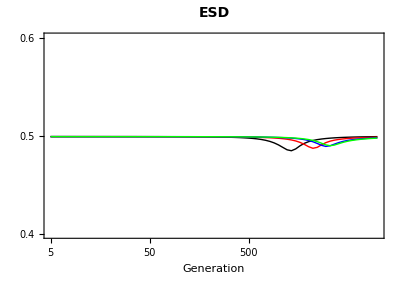

```mathematica
plotB=Show[SRBlack,SRRed,SRBlue,SRGreen,
ImagePadding->Pad,
FrameLabel->{{Style["",FontSize->14],""},{Style["Generation",FontSize->14],""}},
Epilog->{Inset[Show[MODBlack,MODRed,MODBlue,MODGreen,(*ImageSize->150,*)BaseStyle->{TextStyle->Bold,FontFamily->"Helvetica",FontSize->8},
FrameLabel->{{Style["freq ESD",FontSize->8],""},{Style["",FontSize->14],""}}],
Scaled@{1.05,-0.15},{Right,Bottom},{3.4,3.4*Sqrt[2]}],
Text[Style["ESD",Bold,14],Scaled@{0.5,1.1}]}
]
```

## Plot: sex determiner dynamics

### Parameters

```mathematica
yplotmin=-0.075;
yplotmax=0.15;
yplotinterval=0.02;
```

```mathematica
Pad={{50,20},{40,30}};  (*space around plot*)
letpos={.05,.93};  (*relative location of letter, eg A, in figure*)
ylabpos={-0.175,0.5};  (*relative location of y axis label position*)
```

```mathematica
(*{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}*)
```

```mathematica
modvec1={0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0}; (*fraction male with ESD*)
modvec2={0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1}; (*fraction female with ESD*)
modvec3={1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0}; (*fraction male with Z*)
modvec4={0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0}; (*fraction female with Z*)
modvec5={0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0}; (*fraction male with W*)
modvec6={0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1}; (*fraction female with W*)
```

```mathematica
loglinearplotINVoptions={Frame->{{True,False},{True,False}}, 
PlotRangeClipping->False,
ImagePadding->Pad,
FrameStyle->Directive[Black,Thickness[lwd]],
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameTicks->{{{5,5,{0,0.01}},{10,10,{0,0.01}},{100,100,{0,0.01}},{1000,1000,{0,0.01}}},Table[{y,y,ticksize},{y,0,1,0.5}]},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
ImageSize->{xsize,xsize aspectratio},
AspectRatio->aspectratio,
Axes->True};
```

```mathematica
loglinearplotINVSRoptions={Frame->{{True,False},{True,False}}, 
PlotRangeClipping->False,
ImagePadding->Pad,
FrameStyle->Directive[Black,Thickness[lwd]],
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameTicks->{{{5,5,{0,0.01}},{10,10,{0,0.01}},{50,50,{0,0.01}},{100,100,{0,0.01}},{500,500,{0,0.01}},{1000,1000,{0,0.01}}},Table[{y,y,ticksize},{y,0.4,0.6,0.1}]},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
Axes->True};
```

### sex determiner frequencies

#### Parameters

```mathematica
startplot=5;
endtime=20000;
trypm=0.01;
tryk=1/2;
```

```mathematica
trys=0.2;
tryh=0.7;
tryαDm=-0.1;
tryFAA=1+trys ;
tryFAa=1+trys tryh;
tryFaa=1;
tryMAA=1+trys;
tryMAa=1+trys tryh;
tryMaa=1;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5+tryαDm;
tryαm=0.5;
tryr=0.02;
subpar1={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

#### Plots

```mathematica
modvec=modvec1
```

{0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0}

```mathematica
tryR=0.001;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab2Black=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODBlack=ListLogLinearPlot[MODtab2Black,Joined->True,PlotRange->{{startplot,endtime},{0,1.05}},PlotStyle->{Black},loglinearplotINVoptions];
```

```mathematica
tryR=0.02;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtabRed=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODRed=ListLogLinearPlot[MODtabRed,Joined->True,PlotRange->{{startplot,endtime},{0,1.05}},PlotStyle->{Red},loglinearplotINVoptions];
```

```mathematica
tryR=0.1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtabBlue=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODBlue=ListLogLinearPlot[MODtabBlue,Joined->True,PlotRange->{{startplot,endtime},{0,1.05}},PlotStyle->{Blue},loglinearplotINVoptions];
```

```mathematica
tryR=0.5;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtabGreen=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODGreen=ListLogLinearPlot[MODtabGreen,Joined->True,PlotRange->{{startplot,endtime},{0,1.05}},PlotStyle->{Green},loglinearplotINVoptions];
```

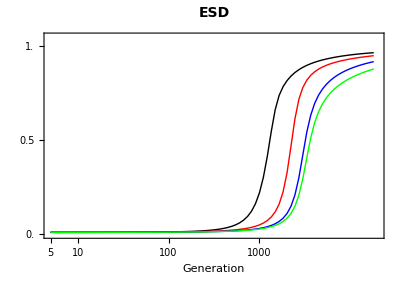

```mathematica
plotA=Show[MODBlack,MODRed,MODBlue,MODGreen,
ImagePadding->Pad,
FrameLabel->{{Style["",FontSize->14],""},{Style["Generation",FontSize->14],""}},
Epilog->Text[Style["ESD",Bold,14],Scaled@{0.5,1.1}]
]
```

#### Plots

```mathematica
modvec=modvec2
```

{0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1}

```mathematica
tryR=0.001;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab2Black=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODBlack=ListLogLinearPlot[MODtab2Black,Joined->True,PlotRange->{{startplot,endtime},{0,1.05}},PlotStyle->{Black,Dashed},loglinearplotINVoptions];
```

```mathematica
tryR=0.02;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtabRed=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODRed=ListLogLinearPlot[MODtabRed,Joined->True,PlotRange->{{startplot,endtime},{0,1.05}},PlotStyle->{Red,Dashed},loglinearplotINVoptions];
```

```mathematica
tryR=0.1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtabBlue=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODBlue=ListLogLinearPlot[MODtabBlue,Joined->True,PlotRange->{{startplot,endtime},{0,1.05}},PlotStyle->{Blue,Dashed},loglinearplotINVoptions];
```

```mathematica
tryR=0.5;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtabGreen=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODGreen=ListLogLinearPlot[MODtabGreen,Joined->True,PlotRange->{{startplot,endtime},{0,1.05}},PlotStyle->{Green,Dashed},loglinearplotINVoptions];
```

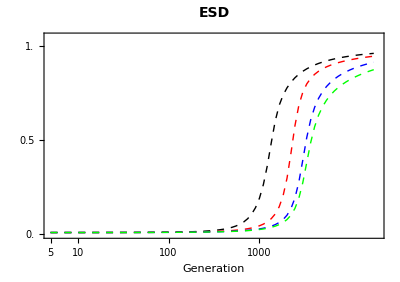

```mathematica
plotB=Show[MODBlack,MODRed,MODBlue,MODGreen,
ImagePadding->Pad,
FrameLabel->{{Style["",FontSize->14],""},{Style["Generation",FontSize->14],""}},
Epilog->Text[Style["ESD",Bold,14],Scaled@{0.5,1.1}]
]
```

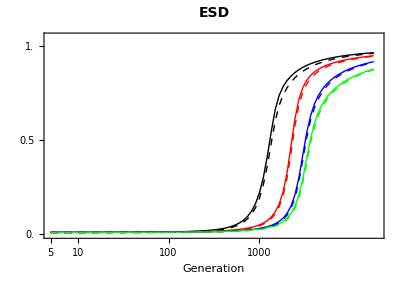

```mathematica
Show[plotA,plotB]
```